# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.752505,0.713769,0.677341,0.643289,0.611593,0.582172,0.554906,0.529655,0.50627,0.484602,0.464507,0.44585,0.428504,0.412353,0.397292,0.383225,0.370065,0.357734,0.346161}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.468843,0.480929,0.493555,0.50692,0.521196,0.536532,0.553056,0.570883,0.590122,0.610871,0.633231,0.6573,0.68318,0.710977,0.740801,0.772771,0.807012,0.843659,0.882856}

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

FAINT

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 30% Bright (m=10/3)

```mathematica
m=10/3;
```

```mathematica
db=1.2;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[10/3, dbz]
```

{1.46304,1.51379,1.56867,1.62801,1.69219,1.7616,1.83666,1.91784,2.00563,2.10056,2.20323,2.31426,2.43434,2.56419,2.70462,2.85649,3.02073,3.19834,3.39042}

```mathematica
bFzSKA30=bF[10/3,dbz]
```

{0.263042,0.313787,0.368665,0.428013,0.492194,0.561603,0.636665,0.71784,0.805627,0.900564,1.00323,1.11426,1.23434,1.36419,1.50462,1.65649,1.82073,1.99834,2.19042}

```mathematica
bTzSKA30 = bT[10/3,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA30 = 3/10;
```

```mathematica
smodelBzSKA30 = List[0.63665525,0.42367658,0.50881959,0.60522562,0.67778459,0.73405886,0.78698648,0.85067709,0.92313678,1.00034598,1.07877756,1.15621473,1.23564294,1.31904933,1.40610202,1.49646092,1.58855833,1.68141612,1.77443344];
```

```mathematica
fevolBzSKA30 = List[-2.35710791,0.50267603,0.00895782,-0.59492009,-0.49505863,-0.16404253,0.19264397,0.36952203,0.43853907,0.45440814,0.4833308,0.54007682,0.59932034,0.6323595,0.65280044,0.66681915,0.69110994,0.7429895,0.81482988];
```

FAINT

```mathematica
nFSKA30 = 7/10;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

10/3

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.128184,0.0583469,0.133246,0.226934,0.34323,0.467545,0.587359,0.69865,0.803523,0.904826,1.00684,1.11062,1.21737,1.32493,1.43485,1.54726,1.6627,1.78189,1.90084}

```mathematica
fevolFzSKA30 = List[4.22894971,3.22955823,2.61765473,1.95918753,0.94948372,0.01885715,-0.72267224,-1.22839524,-1.57209693,-1.82896117,-2.03473879,-2.22488036,-2.39749383,-2.54686948,-2.68379003,-2.81081826,-2.93482756,-3.05441667,-3.14524578];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
nFzSKA30
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0600505,0.0351586,0.0209208,0.0126881,0.00781626,0.00494933,0.00316718,0.00204366,0.00131724,0.000842645,0.000538518,0.000341901,0.00021502,0.000134629,0.0000828116,0.000050365,0.000030219,0.0000177246,0.0000101699}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.140118,0.0820368,0.0488153,0.0296056,0.0182379,0.0115484,0.00739009,0.00476853,0.00307355,0.00196617,0.00125654,0.000797768,0.000501713,0.000314135,0.000193227,0.000117518,0.000070511,0.0000413574,0.0000237297}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{2.9008×10^-8,1.81879×10^-8,1.57546×10^-8,1.58995×10^-8,1.75318×10^-8,2.01724×10^-8,2.41537×10^-8,2.97893×10^-8,3.78812×10^-8,4.9692×10^-8,6.65124×10^-8,9.10478×10^-8,1.2751×10^-7,1.81406×10^-7,2.65268×10^-7,3.95622×10^-7,6.0248×10^-7,9.44614×10^-7,1.52263×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{1.2432×10^-8,7.79481×10^-9,6.75196×10^-9,6.81408×10^-9,7.51364×10^-9,8.64533×10^-9,1.03516×10^-8,1.27668×10^-8,1.62348×10^-8,2.12966×10^-8,2.85053×10^-8,3.90205×10^-8,5.46473×10^-8,7.77456×10^-8,1.13686×10^-7,1.69552×10^-7,2.58206×10^-7,4.04834×10^-7,6.52554×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{-1.70391,0.895284,0.592824,0.630427,0.480152,0.279389,0.0786685,0.00333885,0.0248213,0.116481,0.226818,0.340321,0.472092,0.646354,0.851276,1.08106,1.31899,1.54657,1.7686}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{9.13213,3.51792,2.0517,1.29866,1.16499,1.29248,1.54051,1.79292,2.04051,2.30254,2.58099,2.8947,3.23377,3.58883,3.964,4.35837,4.77599,5.21419,5.6457}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.94878×10^-9,3.1572×10^-9,1.75438×10^-9,1.15557×10^-9,8.44732×10^-10,6.63392×10^-10,5.49527×10^-10,4.74745×10^-10,4.24553×10^-10,3.9096×10^-10,3.69318×10^-10,3.56839×10^-10,3.51849×10^-10,3.53384×10^-10,3.60974×10^-10,3.74522×10^-10,3.94238×10^-10,4.20619×10^-10,4.54445×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{7.94878×10^-9,3.1572×10^-9,1.75438×10^-9,1.15557×10^-9,8.44732×10^-10,6.63392×10^-10,5.49527×10^-10,4.74745×10^-10,4.24553×10^-10,3.9096×10^-10,3.69318×10^-10,3.56839×10^-10,3.51849×10^-10,3.53384×10^-10,3.60974×10^-10,3.74522×10^-10,3.94238×10^-10,4.20619×10^-10,4.54445×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{9.2376×10^-11,5.17657×10^-11,3.84642×10^-11,3.25606×10^-11,2.96946×10^-11,2.84454×10^-11,2.82484×10^-11,2.88623×10^-11,3.01951×10^-11,3.22376×10^-11,3.50369×10^-11,3.86865×10^-11,4.33257×10^-11,4.91428×10^-11,5.63846×10^-11,6.53676×10^-11,7.64955×10^-11,9.02809×10^-11,1.07374×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{9.2376×10^-11,5.17657×10^-11,3.84642×10^-11,3.25606×10^-11,2.96946×10^-11,2.84454×10^-11,2.82484×10^-11,2.88623×10^-11,3.01951×10^-11,3.22376×10^-11,3.50369×10^-11,3.86865×10^-11,4.33257×10^-11,4.91428×10^-11,5.63846×10^-11,6.53676×10^-11,7.64955×10^-11,9.02809×10^-11,1.07374×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{7.55661×10^-10,3.64491×10^-10,2.38394×10^-10,1.80614×10^-10,1.49263×10^-10,1.30785×10^-10,1.19642×10^-10,1.13223×10^-10,1.10186×10^-10,1.09815×10^-10,1.11745×10^-10,1.15828×10^-10,1.2207×10^-10,1.30598×10^-10,1.41655×10^-10,1.55597×10^-10,1.72907×10^-10,1.94214×10^-10,2.20323×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.55661×10^-10,3.64491×10^-10,2.38394×10^-10,1.80614×10^-10,1.49263×10^-10,1.30785×10^-10,1.19642×10^-10,1.13223×10^-10,1.10186×10^-10,1.09815×10^-10,1.11745×10^-10,1.15828×10^-10,1.2207×10^-10,1.30598×10^-10,1.41655×10^-10,1.55597×10^-10,1.72907×10^-10,1.94214×10^-10,2.20323×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.4614×10^-9,1.06866×10^-9,6.4079×10^-10,4.51002×10^-10,3.49635×10^-10,2.89492×10^-10,2.51663×10^-10,2.27326×10^-10,2.11916×10^-10,2.02913×10^-10,1.98876×10^-10,1.98989×10^-10,2.02835×10^-10,2.10271×10^-10,2.21368×10^-10,2.36382×10^-10,2.55748×10^-10,2.80089×10^-10,3.1024×10^-10}

```mathematica
coeffvarCC30BFx50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.4614×10^-9,1.06866×10^-9,6.4079×10^-10,4.51002×10^-10,3.49635×10^-10,2.89492×10^-10,2.51663×10^-10,2.27326×10^-10,2.11916×10^-10,2.02913×10^-10,1.98876×10^-10,1.98989×10^-10,2.02835×10^-10,2.10271×10^-10,2.21368×10^-10,2.36382×10^-10,2.55748×10^-10,2.80089×10^-10,3.1024×10^-10}

```mathematica
coeffvarCC50Fx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.53269×10^-10,1.33216×10^-10,9.3726×10^-11,7.56198×10^-11,6.60532×10^-11,6.08266×10^-11,5.82274×10^-11,5.74659×10^-11,5.81628×10^-11,6.01508×10^-11,6.33905×10^-11,6.79321×10^-11,7.39001×10^-11,8.14901×10^-11,9.09733×10^-11,1.02707×10^-10,1.17151×10^-10,1.3489×10^-10,1.56665×10^-10}

```mathematica
coeffvarCC30BFx50F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.53269×10^-10,1.33216×10^-10,9.3726×10^-11,7.56198×10^-11,6.60532×10^-11,6.08266×10^-11,5.82274×10^-11,5.74659×10^-11,5.81628×10^-11,6.01508×10^-11,6.33905×10^-11,6.79321×10^-11,7.39001×10^-11,8.14901×10^-11,9.09733×10^-11,1.02707×10^-10,1.17151×10^-10,1.3489×10^-10,1.56665×10^-10}

```mathematica
coeffvarCC30Bx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.24247×10^-9,1.00706×10^-9,6.18595×10^-10,4.43202×10^-10,3.48255×10^-10,2.91368×10^-10,2.55368×10^-10,2.32158×10^-10,2.1752×10^-10,2.09107×10^-10,2.05576×10^-10,2.0617×10^-10,2.10508×10^-10,2.18472×10^-10,2.30156×10^-10,2.45833×10^-10,2.65955×10^-10,2.91163×10^-10,3.22313×10^-10}

```mathematica
coeffvarCC50BFx30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.24247×10^-9,1.00706×10^-9,6.18595×10^-10,4.43202×10^-10,3.48255×10^-10,2.91368×10^-10,2.55368×10^-10,2.32158×10^-10,2.1752×10^-10,2.09107×10^-10,2.05576×10^-10,2.0617×10^-10,2.10508×10^-10,2.18472×10^-10,2.30156×10^-10,2.45833×10^-10,2.65955×10^-10,2.91163×10^-10,3.22313×10^-10}

```mathematica
coeffvarCC30Fx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.64934×10^-10,1.36713×10^-10,9.48189×10^-11,7.56638×10^-11,6.55215×10^-11,5.99196×10^-11,5.70373×10^-11,5.60337×10^-11,5.65017×10^-11,5.82572×10^-11,6.12483×10^-11,6.55156×10^-11,7.1175×10^-11,7.84133×10^-11,8.74922×10^-11,9.87586×10^-11,1.1266×10^-10,1.29769×10^-10,1.50809×10^-10}

```mathematica
coeffvarCC50BFx30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.64934×10^-10,1.36713×10^-10,9.48189×10^-11,7.56638×10^-11,6.55215×10^-11,5.99196×10^-11,5.70373×10^-11,5.60337×10^-11,5.65017×10^-11,5.82572×10^-11,6.12483×10^-11,6.55156×10^-11,7.1175×10^-11,7.84133×10^-11,8.74922×10^-11,9.87586×10^-11,1.1266×10^-10,1.29769×10^-10,1.50809×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50Fx30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50FLp4d4to172zSKA= Table[coeffvarCC30BFx50F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30Fx50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30FLp4d4to172zSKA= Table[coeffvarCC50BFx30F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{8.0936×10^-10,3.80267×10^-10,2.44006×10^-10,1.82234×10^-10,1.4895×10^-10,1.29386×10^-10,1.17551×10^-10,1.10634×10^-10,1.07193×10^-10,1.0646×10^-10,1.08036×10^-10,1.11751×10^-10,1.17594×10^-10,1.25681×10^-10,1.36241×10^-10,1.49616×10^-10,1.66276×10^-10,1.86834×10^-10,2.1208×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.0936×10^-10,3.80267×10^-10,2.44006×10^-10,1.82234×10^-10,1.4895×10^-10,1.29386×10^-10,1.17551×10^-10,1.10634×10^-10,1.07193×10^-10,1.0646×10^-10,1.08036×10^-10,1.11751×10^-10,1.17594×10^-10,1.25681×10^-10,1.36241×10^-10,1.49616×10^-10,1.66276×10^-10,1.86834×10^-10,2.1208×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.12242×10^-10,3.5132×10^-10,2.33694×10^-10,1.79376×10^-10,1.49767×10^-10,1.32302×10^-10,1.21828×10^-10,1.15906×10^-10,1.1328×10^-10,1.13286×10^-10,1.15587×10^-10,1.20057×10^-10,1.26717×10^-10,1.35708×10^-10,1.47285×10^-10,1.61818×10^-10,1.79803×10^-10,2.01885×10^-10,2.28888×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{7.12242×10^-10,3.5132×10^-10,2.33694×10^-10,1.79376×10^-10,1.49767×10^-10,1.32302×10^-10,1.21828×10^-10,1.15906×10^-10,1.1328×10^-10,1.13286×10^-10,1.15587×10^-10,1.20057×10^-10,1.26717×10^-10,1.35708×10^-10,1.47285×10^-10,1.61818×10^-10,1.79803×10^-10,2.01885×10^-10,2.28888×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BFx30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.89646×10^-8,1.14786×10^-9,1.27856×10^-10,2.43593×10^-11,1.84677×10^-11,2.173×10^-11,2.76709×10^-11,3.45278×10^-11,4.07091×10^-11,4.50542×10^-11,4.72366×10^-11,4.77075×10^-11,4.78791×10^-11,4.79338×10^-11,4.88575×10^-11,5.08852×10^-11,5.44991×10^-11,6.01889×10^-11,6.65643×10^-11}

```mathematica
coeffvarCC30BFx50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.89646×10^-8,1.14786×10^-9,1.27856×10^-10,2.43593×10^-11,1.84677×10^-11,2.173×10^-11,2.76709×10^-11,3.45278×10^-11,4.07091×10^-11,4.50542×10^-11,4.72366×10^-11,4.77075×10^-11,4.78791×10^-11,4.79338×10^-11,4.88575×10^-11,5.08852×10^-11,5.44991×10^-11,6.01889×10^-11,6.65643×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BFx30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BFx50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.2209×10^-9,8.91882×10^-10,4.98951×10^-10,3.29662×10^-10,2.40981×10^-10,1.88754×10^-10,1.5561×10^-10,1.33554×10^-10,1.18481×10^-10,1.08109×10^-10,1.01098×10^-10,9.66304×10^-11,9.42029×10^-11,9.35099×10^-11,9.43813×10^-11,9.67461×10^-11,1.00613×10^-10,1.06061×10^-10,1.13236×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.5023×10^-11,2.44463×10^-11,1.76038×10^-11,1.44359×10^-11,1.27449×10^-11,1.18099×10^-11,1.13372×10^-11,1.11918×10^-11,1.13095×10^-11,1.16628×10^-11,1.22466×10^-11,1.30718×10^-11,1.41628×10^-11,1.5557×10^-11,1.73063×10^-11,1.94787×10^-11,2.21617×10^-11,2.54671×10^-11,2.95365×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.2209×10^-9,8.91882×10^-10,4.98951×10^-10,3.29662×10^-10,2.40981×10^-10,1.88754×10^-10,1.5561×10^-10,1.33554×10^-10,1.18481×10^-10,1.08109×10^-10,1.01098×10^-10,9.66304×10^-11,9.42029×10^-11,9.35099×10^-11,9.43813×10^-11,9.67461×10^-11,1.00613×10^-10,1.06061×10^-10,1.13236×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{4.5023×10^-11,2.44463×10^-11,1.76038×10^-11,1.44359×10^-11,1.27449×10^-11,1.18099×10^-11,1.13372×10^-11,1.11918×10^-11,1.13095×10^-11,1.16628×10^-11,1.22466×10^-11,1.30718×10^-11,1.41628×10^-11,1.5557×10^-11,1.73063×10^-11,1.94787×10^-11,2.21617×10^-11,2.54671×10^-11,2.95365×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.03918×10^-10,1.40962×10^-10,8.91142×10^-11,6.54497×10^-11,5.25218×10^-11,4.47312×10^-11,3.98011×10^-11,3.66556×10^-11,3.47338×10^-11,3.37255×10^-11,3.34562×10^-11,3.38323×10^-11,3.48136×10^-11,3.63992×10^-11,3.86204×10^-11,4.15386×10^-11,4.5246×10^-11,4.98683×10^-11,5.55703×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.9115×10^-10,1.3927×10^-10,9.00345×10^-11,6.72341×10^-11,5.46404×10^-11,4.69932×10^-11,4.21352×10^-11,3.90395×10^-11,3.71674×10^-11,3.622×10^-11,3.60292×10^-11,3.65055×10^-11,3.76121×10^-11,3.93513×10^-11,4.17579×10^-11,4.48975×10^-11,4.88667×10^-11,5.37971×10^-11,5.98602×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.9115×10^-10,1.3927×10^-10,9.00345×10^-11,6.72341×10^-11,5.46404×10^-11,4.69932×10^-11,4.21352×10^-11,3.90395×10^-11,3.71674×10^-11,3.622×10^-11,3.60292×10^-11,3.65055×10^-11,3.76121×10^-11,3.93513×10^-11,4.17579×10^-11,4.48975×10^-11,4.88667×10^-11,5.37971×10^-11,5.98602×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.03918×10^-10,1.40962×10^-10,8.91142×10^-11,6.54497×10^-11,5.25218×10^-11,4.47312×10^-11,3.98011×10^-11,3.66556×10^-11,3.47338×10^-11,3.37255×10^-11,3.34562×10^-11,3.38323×10^-11,3.48136×10^-11,3.63992×10^-11,3.86204×10^-11,4.15386×10^-11,4.5246×10^-11,4.98683×10^-11,5.55703×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.96798×10^-10,1.3992×10^-10,8.94952×10^-11,6.6299×10^-11,5.35515×10^-11,4.58378×10^-11,4.09456×10^-11,3.78254×10^-11,3.59281×10^-11,3.49494×10^-11,3.47183×10^-11,3.51432×10^-11,3.61857×10^-11,3.78464×10^-11,4.01585×10^-11,4.31854×10^-11,4.70215×10^-11,5.17954×10^-11,5.76753×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.96798×10^-10,1.3992×10^-10,8.94952×10^-11,6.6299×10^-11,5.35515×10^-11,4.58378×10^-11,4.09456×10^-11,3.78254×10^-11,3.59281×10^-11,3.49494×10^-11,3.47183×10^-11,3.51432×10^-11,3.61857×10^-11,3.78464×10^-11,4.01585×10^-11,4.31854×10^-11,4.70215×10^-11,5.17954×10^-11,5.76753×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.04961×10^-10,3.48573×10^-10,2.07858×10^-10,1.45116×10^-10,1.1135×10^-10,9.1088×10^-11,7.81181×10^-11,6.95312×10^-11,6.38127×10^-11,6.0115×10^-11,5.79423×10^-11,5.70006×10^-11,5.71208×10^-11,5.82181×10^-11,6.02698×10^-11,6.33039×10^-11,6.7394×10^-11,7.26591×10^-11,7.92672×10^-11}

```mathematica
coeffvarCC30BFx50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.04961×10^-10,3.48573×10^-10,2.07858×10^-10,1.45116×10^-10,1.1135×10^-10,9.1088×10^-11,7.81181×10^-11,6.95312×10^-11,6.38127×10^-11,6.0115×10^-11,5.79423×10^-11,5.70006×10^-11,5.71208×10^-11,5.82181×10^-11,6.02698×10^-11,6.33039×10^-11,6.7394×10^-11,7.26591×10^-11,7.92672×10^-11}

```mathematica
coeffvarCC50Fx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.14028×10^-10,5.80996×10^-11,3.96379×10^-11,3.10194×10^-11,2.6278×10^-11,2.34634×10^-11,2.17736×10^-11,2.08294×10^-11,2.04366×10^-11,2.04937×10^-11,2.09517×10^-11,2.17955×10^-11,2.3035×10^-11,2.4701×10^-11,2.68444×10^-11,2.95373×10^-11,3.28758×10^-11,3.6984×10^-11,4.20202×10^-11}

```mathematica
coeffvarCC30BFx50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.14028×10^-10,5.80996×10^-11,3.96379×10^-11,3.10194×10^-11,2.6278×10^-11,2.34634×10^-11,2.17736×10^-11,2.08294×10^-11,2.04366×10^-11,2.04937×10^-11,2.09517×10^-11,2.17955×10^-11,2.3035×10^-11,2.4701×10^-11,2.68444×10^-11,2.95373×10^-11,3.28758×10^-11,3.6984×10^-11,4.20202×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30Bx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.75361×10^-10,3.42618×10^-10,2.07265×10^-10,1.46234×10^-10,1.13098×10^-10,9.30786×10^-11,8.01993×10^-11,7.16437×10^-11,6.59373×10^-11,6.22511×10^-11,6.00986×10^-11,5.91905×10^-11,5.93608×10^-11,6.05268×10^-11,6.26678×10^-11,6.58137×10^-11,7.00405×10^-11,7.54701×10^-11,8.22737×10^-11}

```mathematica
coeffvarCC50BFx30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.75361×10^-10,3.42618×10^-10,2.07265×10^-10,1.46234×10^-10,1.13098×10^-10,9.30786×10^-11,8.01993×10^-11,7.16437×10^-11,6.59373×10^-11,6.22511×10^-11,6.00986×10^-11,5.91905×10^-11,5.93608×10^-11,6.05268×10^-11,6.26678×10^-11,6.58137×10^-11,7.00405×10^-11,7.54701×10^-11,8.22737×10^-11}

```mathematica
coeffvarCC30Fx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.15615×10^-10,5.81091×10^-11,3.92561×10^-11,3.04976×10^-11,2.56937×10^-11,2.28441×10^-11,2.11286×10^-11,2.01598×10^-11,1.97393×10^-11,1.97633×10^-11,2.01812×10^-11,2.09765×10^-11,2.21578×10^-11,2.37543×10^-11,2.58153×10^-11,2.84111×10^-11,3.16352×10^-11,3.56092×10^-11,4.04883×10^-11}

```mathematica
coeffvarCC50BFx30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.15615×10^-10,5.81091×10^-11,3.92561×10^-11,3.04976×10^-11,2.56937×10^-11,2.28441×10^-11,2.11286×10^-11,2.01598×10^-11,1.97393×10^-11,1.97633×10^-11,2.01812×10^-11,2.09765×10^-11,2.21578×10^-11,2.37543×10^-11,2.58153×10^-11,2.84111×10^-11,3.16352×10^-11,3.56092×10^-11,4.04883×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{5.88449×10^-27,-5.32466×10^-28,3.08938×10^-27,-3.82043×10^-27,-2.1949×10^-27,-7.74279×10^-28,-6.92995×10^-29,3.23798×10^-28,1.6639×10^-27,7.58586×10^-28,-4.7999×10^-28,9.06183×10^-28,4.21274×10^-27,-7.38452×10^-28,2.13082×10^-27,-3.35176×10^-27,-2.32119×10^-27,-3.41792×10^-28,-1.72255×10^-27}

```mathematica
coeffvarCCOCT50BFx30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{1.09966×10^-8,4.31725×10^-10,4.76497×10^-11,9.01537×10^-12,6.92086×10^-12,8.21427×10^-12,1.05044×10^-11,1.31307×10^-11,1.5483×10^-11,1.71169×10^-11,1.79159×10^-11,1.80569×10^-11,1.80826×10^-11,1.80633×10^-11,1.83737×10^-11,1.91012×10^-11,2.04259×10^-11,2.25296×10^-11,2.48867×10^-11}

```mathematica
coeffvarCCOCT30BFx50BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{1.09966×10^-8,4.31725×10^-10,4.76497×10^-11,9.01537×10^-12,6.92086×10^-12,8.21427×10^-12,1.05044×10^-11,1.31307×10^-11,1.5483×10^-11,1.71169×10^-11,1.79159×10^-11,1.80569×10^-11,1.80826×10^-11,1.80633×10^-11,1.83737×10^-11,1.91012×10^-11,2.04259×10^-11,2.25296×10^-11,2.48867×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BFx30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCOCT30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCCOCT30BFx50BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

We use the HEXADECAPOLE of the TOTAL POPULATION (for each splitting, same total population)

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50Tx30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30Tx50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCC50Tx30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCC30Tx50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50Bx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-9.17898×10^-9,-3.76713×10^-9,-2.13465×10^-9,-1.41847×10^-9,-1.03681×10^-9,-8.0811×10^-10,-6.60179×10^-10,-5.59421×10^-10,-4.88374×10^-10,-4.37191×10^-10,-3.99969×10^-10,-3.73004×10^-10,-3.53892×10^-10,-3.4104×10^-10,-3.33383×10^-10,-3.30218×10^-10,-3.31102×10^-10,-3.35785×10^-10,-3.44169×10^-10}

```mathematica
coeffvarCC30Bx50B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-9.17898×10^-9,-3.76713×10^-9,-2.13465×10^-9,-1.41847×10^-9,-1.03681×10^-9,-8.0811×10^-10,-6.60179×10^-10,-5.59421×10^-10,-4.88374×10^-10,-4.37191×10^-10,-3.99969×10^-10,-3.73004×10^-10,-3.53892×10^-10,-3.4104×10^-10,-3.33383×10^-10,-3.30218×10^-10,-3.31102×10^-10,-3.35785×10^-10,-3.44169×10^-10}

```mathematica
coeffvarCC50Fx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.88329×10^-10,-1.56116×10^-10,-1.11887×10^-10,-9.11287×10^-11,-7.97227×10^-11,-7.30176×10^-11,-6.90904×10^-11,-6.70266×10^-11,-6.63526×10^-11,-6.68136×10^-11,-6.82769×10^-11,-7.06849×10^-11,-7.40318×10^-11,-7.83518×10^-11,-8.37132×10^-11,-9.02164×10^-11,-9.79945×10^-11,-1.07216×10^-10,-1.18086×10^-10}

```mathematica
coeffvarCC30Fx50F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-2.88329×10^-10,-1.56116×10^-10,-1.11887×10^-10,-9.11287×10^-11,-7.97227×10^-11,-7.30176×10^-11,-6.90904×10^-11,-6.70266×10^-11,-6.63526×10^-11,-6.68136×10^-11,-6.82769×10^-11,-7.06849×10^-11,-7.40318×10^-11,-7.83518×10^-11,-8.37132×10^-11,-9.02164×10^-11,-9.79945×10^-11,-1.07216×10^-10,-1.18086×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50Bx30B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30Bx50B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50Fx30F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30Fx50F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250Bx30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.81085×10^-9,-8.31248×10^-10,-5.19297×10^-10,-3.7622×10^-10,-2.97224×10^-10,-2.48681×10^-10,-2.16891×10^-10,-1.95339×10^-10,-1.80576×10^-10,-1.70633×10^-10,-1.64326×10^-10,-1.60922×10^-10,-1.59963×10^-10,-1.61173×10^-10,-1.64405×10^-10,-1.69605×10^-10,-1.76797×10^-10,-1.86074×10^-10,-1.97589×10^-10}

```mathematica
coeffvarCC0230Fx50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.81085×10^-9,-8.31248×10^-10,-5.19297×10^-10,-3.7622×10^-10,-2.97224×10^-10,-2.48681×10^-10,-2.16891×10^-10,-1.95339×10^-10,-1.80576×10^-10,-1.70633×10^-10,-1.64326×10^-10,-1.60922×10^-10,-1.59963×10^-10,-1.61173×10^-10,-1.64405×10^-10,-1.69605×10^-10,-1.76797×10^-10,-1.86074×10^-10,-1.97589×10^-10}

```mathematica
coeffvarCC0230Bx50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.83969×10^-9,-8.64809×10^-10,-5.49033×10^-10,-4.02208×10^-10,-3.20216×10^-10,-2.69345×10^-10,-2.35748×10^-10,-2.1279×10^-10,-1.96935×10^-10,-1.8615×10^-10,-1.79205×10^-10,-1.75331×10^-10,-1.74045×10^-10,-1.75053×10^-10,-1.78194×10^-10,-1.83404×10^-10,-1.907×10^-10,-2.00169×10^-10,-2.11964×10^-10}

```mathematica
coeffvarCC0250Fx30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.83969×10^-9,-8.64809×10^-10,-5.49033×10^-10,-4.02208×10^-10,-3.20216×10^-10,-2.69345×10^-10,-2.35748×10^-10,-2.1279×10^-10,-1.96935×10^-10,-1.8615×10^-10,-1.79205×10^-10,-1.75331×10^-10,-1.74045×10^-10,-1.75053×10^-10,-1.78194×10^-10,-1.83404×10^-10,-1.907×10^-10,-2.00169×10^-10,-2.11964×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250Bx30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230Fx50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230Bx50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250Fx30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BFx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.8329×10^-9,-8.50133×10^-10,-5.34892×10^-10,-3.89449×10^-10,-3.08746×10^-10,-2.58942×10^-10,-2.26201×10^-10,-2.03924×10^-10,-1.88605×10^-10,-1.78239×10^-10,-1.71613×10^-10,-1.67977×10^-10,-1.66857×10^-10,-1.67971×10^-10,-1.71161×10^-10,-1.76369×10^-10,-1.83617×10^-10,-1.92993×10^-10,-2.04651×10^-10}

```mathematica
coeffvarCC30BFx50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.8329×10^-9,-8.50133×10^-10,-5.34892×10^-10,-3.89449×10^-10,-3.08746×10^-10,-2.58942×10^-10,-2.26201×10^-10,-2.03924×10^-10,-1.88605×10^-10,-1.78239×10^-10,-1.71613×10^-10,-1.67977×10^-10,-1.66857×10^-10,-1.67971×10^-10,-1.71161×10^-10,-1.76369×10^-10,-1.83617×10^-10,-1.92993×10^-10,-2.04651×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50Bx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-4.29215×10^-9,-1.84713×10^-9,-1.09183×10^-9,-7.53661×10^-10,-5.70336×10^-10,-4.58994×10^-10,-3.86323×10^-10,-3.36663×10^-10,-3.01797×10^-10,-2.77057×10^-10,-2.59633×10^-10,-2.4776×10^-10,-2.403×10^-10,-2.36516×10^-10,-2.35938×10^-10,-2.38284×10^-10,-2.43412×10^-10,-2.51295×10^-10,-2.61998×10^-10}

```mathematica
coeffvarCC30BFx50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-4.29215×10^-9,-1.84713×10^-9,-1.09183×10^-9,-7.53661×10^-10,-5.70336×10^-10,-4.58994×10^-10,-3.86323×10^-10,-3.36663×10^-10,-3.01797×10^-10,-2.77057×10^-10,-2.59633×10^-10,-2.4776×10^-10,-2.403×10^-10,-2.36516×10^-10,-2.35938×10^-10,-2.38284×10^-10,-2.43412×10^-10,-2.51295×10^-10,-2.61998×10^-10}

```mathematica
coeffvarCC30Bx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-4.46889×10^-9,-1.92873×10^-9,-1.14225×10^-9,-7.89427×10^-10,-5.97817×10^-10,-4.81251×10^-10,-4.05046×10^-10,-3.52878×10^-10,-3.16174×10^-10,-2.90057×10^-10,-2.71587×10^-10,-2.58913×10^-10,-2.50844×10^-10,-2.466×10^-10,-2.45685×10^-10,-2.47796×10^-10,-2.52777×10^-10,-2.6059×10^-10,-2.71294×10^-10}

```mathematica
coeffvarCC50BFx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.46889×10^-9,-1.92873×10^-9,-1.14225×10^-9,-7.89427×10^-10,-5.97817×10^-10,-4.81251×10^-10,-4.05046×10^-10,-3.52878×10^-10,-3.16174×10^-10,-2.90057×10^-10,-2.71587×10^-10,-2.58913×10^-10,-2.50844×10^-10,-2.466×10^-10,-2.45685×10^-10,-2.47796×10^-10,-2.52777×10^-10,-2.6059×10^-10,-2.71294×10^-10}

```mathematica
coeffvarCC50BFx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-7.33369×10^-10,-3.65175×10^-10,-2.44102×10^-10,-1.87343×10^-10,-1.55623×10^-10,-1.36129×10^-10,-1.23576×10^-10,-1.15432×10^-10,-1.10351×10^-10,-1.07573×10^-10,-1.0665×10^-10,-1.07321×10^-10,-1.09442×10^-10,-1.12955×10^-10,-1.17861×10^-10,-1.24214×10^-10,-1.32117×10^-10,-1.41716×10^-10,-1.53203×10^-10}

```mathematica
coeffvarCC30Fx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-7.33369×10^-10,-3.65175×10^-10,-2.44102×10^-10,-1.87343×10^-10,-1.55623×10^-10,-1.36129×10^-10,-1.23576×10^-10,-1.15432×10^-10,-1.10351×10^-10,-1.07573×10^-10,-1.0665×10^-10,-1.07321×10^-10,-1.09442×10^-10,-1.12955×10^-10,-1.17861×10^-10,-1.24214×10^-10,-1.32117×10^-10,-1.41716×10^-10,-1.53203×10^-10}

```mathematica
coeffvarCC50Fx30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-7.30322×10^-10,-3.6888×10^-10,-2.49035×10^-10,-1.9248×10^-10,-1.60703×10^-10,-1.41087×10^-10,-1.28411×10^-10,-1.20163×10^-10,-1.15007×10^-10,-1.12184×10^-10,-1.11246×10^-10,-1.1193×10^-10,-1.14095×10^-10,-1.17679×10^-10,-1.22684×10^-10,-1.29165×10^-10,-1.37224×10^-10,-1.47008×10^-10,-1.58711×10^-10}

```mathematica
coeffvarCC30BFx50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-7.30322×10^-10,-3.6888×10^-10,-2.49035×10^-10,-1.9248×10^-10,-1.60703×10^-10,-1.41087×10^-10,-1.28411×10^-10,-1.20163×10^-10,-1.15007×10^-10,-1.12184×10^-10,-1.11246×10^-10,-1.1193×10^-10,-1.14095×10^-10,-1.17679×10^-10,-1.22684×10^-10,-1.29165×10^-10,-1.37224×10^-10,-1.47008×10^-10,-1.58711×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50Bx30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30Bx50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.28279×10^-9,5.5453×10^-10,3.26227×10^-10,2.22405×10^-10,1.65157×10^-10,1.29713×10^-10,1.06044×10^-10,8.93931×10^-11,7.72372×10^-11,6.81228×10^-11,6.11572×10^-11,5.57645×10^-11,5.15585×10^-11,4.8272×10^-11,4.57155×10^-11,4.37523×10^-11,4.22824×10^-11,4.1232×10^-11,4.05465×10^-11}

```mathematica
coeffvarCC50Fx30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30Fx50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{3.94109×10^-10,1.8541×10^-10,1.17441×10^-10,8.54876×10^-11,6.7337×10^-11,5.58031×10^-11,4.79326×10^-11,4.23054×10^-11,3.81579×10^-11,3.50441×10^-11,3.26862×10^-11,3.09028×10^-11,2.95711×10^-11,2.86054×10^-11,2.79452×10^-11,2.75469×10^-11,2.73795×10^-11,2.74211×10^-11,2.76568×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BFx30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BFx50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{7.47745×10^-10,3.3492×10^-10,2.03324×10^-10,1.42581×10^-10,1.08629×10^-10,8.73493×10^-11,7.29883×10^-11,6.27986×10^-11,5.53141×10^-11,4.96842×10^-11,4.53831×10^-11,4.20696×10^-11,3.95135×10^-11,3.75549×10^-11,3.60802×10^-11,3.50075×10^-11,3.42771×10^-11,3.38455×10^-11,3.36811×10^-11}

```mathematica
varCCMONO50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50Bx30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50Fx30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30Bx50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.46892×10^-8,-6.26331×10^-9,-3.66835×10^-9,-2.5089×10^-9,-1.881×10^-9,-1.4996×10^-9,-1.25025×10^-9,-1.0792×10^-9,-9.58263×10^-10,-8.71409×10^-10,-8.08971×10^-10,-7.64854×10^-10,-7.35101×10^-10,-7.17109×10^-10,-7.0917×10^-10,-7.102×10^-10,-7.19579×10^-10,-7.3704×10^-10,-7.62616×10^-10}

```mathematica
coeffvarCC30Fx50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-2.91057×10^-9,-1.39402×10^-9,-9.02314×10^-10,-6.73599×10^-10,-5.46001×10^-10,-4.67137×10^-10,-4.15523×10^-10,-3.80889×10^-10,-3.57783×10^-10,-3.43089×10^-10,-3.34948×10^-10,-3.32227×10^-10,-3.34248×10^-10,-3.40643×10^-10,-3.51266×10^-10,-3.66147×10^-10,-3.85465×10^-10,-4.0954×10^-10,-4.38826×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BFx30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BFx50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-6.70666×10^-9,-3.01989×10^-9,-1.85428×10^-9,-1.32208×10^-9,-1.02882×10^-9,-8.48418×10^-10,-7.29694×10^-10,-6.48346×10^-10,-5.91523×10^-10,-5.51872×10^-10,-5.24949×10^-10,-5.07966×10^-10,-4.99147×10^-10,-4.97368×10^-10,-5.01955×10^-10,-5.12561×10^-10,-5.29096×10^-10,-5.51684×10^-10,-5.80639×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BFx30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-2.17127×10^-7,-8.22183×10^-9,-8.74269×10^-10,-1.60119×10^-10,-1.29847×10^-10,-1.59559×10^-10,-2.07293×10^-10,-2.60783×10^-10,-3.07622×10^-10,-3.38761×10^-10,-3.52403×10^-10,-3.52435×10^-10,-3.50014×10^-10,-3.46624×10^-10,-3.4969×10^-10,-3.60812×10^-10,-3.83315×10^-10,-4.2049×10^-10,-4.62117×10^-10}

```mathematica
coeffvarCC30BFx50BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-2.17127×10^-7,-8.22183×10^-9,-8.74269×10^-10,-1.60119×10^-10,-1.29847×10^-10,-1.59559×10^-10,-2.07293×10^-10,-2.60783×10^-10,-3.07622×10^-10,-3.38761×10^-10,-3.52403×10^-10,-3.52435×10^-10,-3.50014×10^-10,-3.46624×10^-10,-3.4969×10^-10,-3.60812×10^-10,-3.83315×10^-10,-4.2049×10^-10,-4.62117×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
((oMP alpha0[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha0[bM, bN,f] ) /nP 
+((-1)^m oMN alpha0[bL,bP,f]  + (-1)^(n+m) oLN alpha0[bM,bP,f])/nN ) G[n,m,0,0] 
+ ((oMP alpha2[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha2[bM, bN,f] ) /nP 
+((-1)^m oMN alpha2[bL,bP,f]  + (-1)^(n+m) oLN alpha2[bM,bP,f])/nN )  G[n,m,2,0] 
+ ((oMP alpha4[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha4[bM, bN,f] ) /nP 
+((-1)^m oMN alpha4[bL,bP,f]  + (-1)^(n+m) oLN alpha4[bM,bP,f])/nN ) G[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
4(alpha0[bL,bP,f] oLP )/nP G[n,m,0,0] + 4(alpha2[bL,bP,f] oLP )/nP G[n,m,2,0] + 4(alpha4[bL,bP,f] oLP)/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJoint[n,m,nN,nP,oLN,oLP,oMN,oMP,bL,bM,bN,bP,f]
coeffvarCPgeneralJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexaHexa[n,m,nN,nP,oLP,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

JOINT ANALYSIS 50X50 - 30X70

```mathematica
OBb = 3/5;
OBf = 2/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nb,oBb,oBb,oBb,oBb,b,b,b,b,f]
```

(b^2 oBb)/nb+(2 b f oBb)/(3 nb)+(f^2 oBb)/(5 nb)

```mathematica
coeffvarCP50Bx30B00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.90215×10^-8,2.67749×10^-8,2.5343×10^-8,2.79198×10^-8,3.35924×10^-8,4.2179×10^-8,5.51435×10^-8,7.43321×10^-8,1.0345×10^-7,1.48763×10^-7,2.18689×10^-7,3.29457×10^-7,5.08896×10^-7,8.00349×10^-7,1.2968×10^-6,2.14812×10^-6,3.64204×10^-6,6.37252×10^-6,0.0000114901}

```mathematica
coeffvarCP50Fx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.29799×10^-9,1.9354×10^-9,2.17982×10^-9,2.79259×10^-9,3.83965×10^-9,5.43536×10^-9,7.92582×10^-9,1.18128×10^-8,1.80456×10^-8,2.83077×10^-8,4.51484×10^-8,7.34371×10^-8,1.21936×10^-7,2.05306×10^-7,3.54787×10^-7,6.24562×10^-7,1.12155×10^-6,2.07179×10^-6,3.93176×10^-6}

```mathematica
coeffvarCP30Bx50B00zSKA=  coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.90215×10^-8,2.67749×10^-8,2.5343×10^-8,2.79198×10^-8,3.35924×10^-8,4.2179×10^-8,5.51435×10^-8,7.43321×10^-8,1.0345×10^-7,1.48763×10^-7,2.18689×10^-7,3.29457×10^-7,5.08896×10^-7,8.00349×10^-7,1.2968×10^-6,2.14812×10^-6,3.64204×10^-6,6.37252×10^-6,0.0000114901}

```mathematica
coeffvarCP30Fx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.29799×10^-9,1.9354×10^-9,2.17982×10^-9,2.79259×10^-9,3.83965×10^-9,5.43536×10^-9,7.92582×10^-9,1.18128×10^-8,1.80456×10^-8,2.83077×10^-8,4.51484×10^-8,7.34371×10^-8,1.21936×10^-7,2.05306×10^-7,3.54787×10^-7,6.24562×10^-7,1.12155×10^-6,2.07179×10^-6,3.93176×10^-6}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nb,nf,bB,bF,bb,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(20 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(12 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(4 nb nf)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(12 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(4 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(20 nb nf)

```mathematica
coeffvarCP50BFx30BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.48853×10^-9,6.02005×10^-9,5.88144×10^-9,6.67975×10^-9,8.27666×10^-9,1.06928×10^-8,1.43732×10^-8,1.99079×10^-8,2.84533×10^-8,4.19987×10^-8,6.33427×10^-8,9.78567×10^-8,1.54927×10^-7,2.49609×10^-7,4.14088×10^-7,7.01878×10^-7,1.21691×10^-6,2.17594×10^-6,4.0066×10^-6}

```mathematica
coeffvarCP30BFx50BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.48853×10^-9,6.02005×10^-9,5.88144×10^-9,6.67975×10^-9,8.27666×10^-9,1.06928×10^-8,1.43732×10^-8,1.99079×10^-8,2.84533×10^-8,4.19987×10^-8,6.33427×10^-8,9.78567×10^-8,1.54927×10^-7,2.49609×10^-7,4.14088×10^-7,7.01878×10^-7,1.21691×10^-6,2.17594×10^-6,4.0066×10^-6}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nN,nP,bL,bL,bN,bP,f]
```

(f^2 (nN+nP) (bL,bN+bL,bP))/(20 nN nP)+(bL (nN+nP) (bP bL,bN+bN bL,bP))/(4 nN nP)+(f (nN+nP) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nN nP)

```mathematica
coeffvarCPgeneralJoint[0,0,nN,nP,oLN,oLP,oLN,oLP,bL,bL,bN,bP,f]
```

(f^2 (nP oLN+nN oLP))/(10 nN nP)+(bL (bP nP oLN+bN nN oLP))/(2 nN nP)+1/6 f (((bL+bP) oLN)/nN+((bL+bN) oLP)/nP)

```mathematica
coeffvarCP50Bx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.12382×10^-8,8.08964×10^-9,7.99541×10^-9,9.16271×10^-9,1.14324×10^-8,1.48482×10^-8,2.00374×10^-8,2.78307×10^-8,3.98492×10^-8,5.88772×10^-8,8.88218×10^-8,1.37169×10^-7,2.16971×10^-7,3.49094×10^-7,5.78117×10^-7,9.77876×10^-7,1.69147×10^-6,3.01677×10^-6,5.53977×10^-6}

```mathematica
coeffvarCP50BFx30B00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.01274×10^-9,3.92995×10^-9,4.15076×10^-9,5.0167×10^-9,6.53901×10^-9,8.80953×10^-9,1.22648×10^-8,1.7499×10^-8,2.56491×10^-8,3.86827×10^-8,5.94235×10^-8,9.32541×10^-8,1.49628×10^-7,2.43824×10^-7,4.08393×10^-7,6.97825×10^-7,1.21803×10^-6,2.19004×10^-6,4.0508×10^-6}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Fx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.58053×10^-9,2.80711×10^-9,2.96483×10^-9,3.58336×10^-9,4.67072×10^-9,6.29252×10^-9,8.76054×10^-9,1.24993×10^-8,1.83208×10^-8,2.76305×10^-8,4.24454×10^-8,6.661×10^-8,1.06877×10^-7,1.7416×10^-7,2.91709×10^-7,4.98447×10^-7,8.70024×10^-7,1.56431×10^-6,2.89343×10^-6}

```mathematica
coeffvarCP50BFx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.50511×10^-9,3.43326×10^-9,3.56095×10^-9,4.25435×10^-9,5.50612×10^-9,7.38896×10^-9,1.02707×10^-8,1.46567×10^-8,2.15167×10^-8,3.25367×10^-8,5.01586×10^-8,7.9047×10^-8,1.27438×10^-7,2.08746×10^-7,3.51572×10^-7,6.042×10^-7,1.06087×10^-6,1.91894×10^-6,3.57087×10^-6}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.23641×10^-9,2.43694×10^-9,2.49999×10^-9,2.95667×10^-9,3.79055×10^-9,5.04151×10^-9,6.94844×10^-9,9.83533×10^-9,1.43261×10^-8,2.15001×10^-8,3.29031×10^-8,5.14876×10^-8,8.24407×10^-8,1.34148×10^-7,2.24492×10^-7,3.8343×10^-7,6.69246×10^-7,1.20366×10^-6,2.22762×10^-6}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nb,nf,bB,bF,bb ,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(28 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(20 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(12 nb nf)

```mathematica
coeffvarCPgeneralJoint[1,1,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb ,bf,f]
```

(f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(28 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(20 nb nf)+(bf bF nf oBb-bb bF nb oBf-bB bf nf oFb+bb bB nb oFf)/(12 nb nf)

```mathematica
coeffvarCP50BFx30BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.94681×10^-9,2.06861×10^-9,1.99927×10^-9,2.24482×10^-9,2.74815×10^-9,3.50596×10^-9,4.65166×10^-9,6.35747×10^-9,8.96418×10^-9,1.30527×10^-8,1.94206×10^-8,2.96017×10^-8,4.62501×10^-8,7.35585×10^-8,1.20507×10^-7,2.01793×10^-7,3.45802×10^-7,6.11431×10^-7,1.11386×10^-6}

```mathematica
coeffvarCP30BFx50BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.94681×10^-9,2.06861×10^-9,1.99927×10^-9,2.24482×10^-9,2.74815×10^-9,3.50596×10^-9,4.65166×10^-9,6.35747×10^-9,8.96418×10^-9,1.30527×10^-8,1.94206×10^-8,2.96017×10^-8,4.62501×10^-8,7.35585×10^-8,1.20507×10^-7,2.01793×10^-7,3.45802×10^-7,6.11431×10^-7,1.11386×10^-6}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneralJoint[2,2,n,n,oBb,oBb,oBb,oBb,Bb,Bb,Bb,Bb,f]
```

(Bb^2 oBb)/(5 n)+(22 Bb f oBb)/(105 n)+(3 f^2 oBb)/(35 n)

```mathematica
coeffvarCP50Bx30B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{9.14312×10^-9,6.30709×10^-9,5.9894×10^-9,6.60829×10^-9,7.95084×10^-9,9.97042×10^-9,1.30047×10^-8,1.74744×10^-8,2.42256×10^-8,3.46834×10^-8,5.07399×10^-8,7.60466×10^-8,1.16833×10^-7,1.82728×10^-7,2.94406×10^-7,4.84913×10^-7,8.17498×10^-7,1.42236×10^-6,2.55043×10^-6}

```mathematica
coeffvarCP50Fx30F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.81563×10^-10,6.36953×10^-10,6.96184×10^-10,8.67139×10^-10,1.16078×10^-9,1.60163×10^-9,2.27884×10^-9,3.31748×10^-9,4.95528×10^-9,7.60863×10^-9,1.18911×10^-8,1.89735×10^-8,3.09379×10^-8,5.12106×10^-8,8.70931×10^-8,1.51041×10^-7,2.67469×10^-7,4.87691×10^-7,9.14373×10^-7}

```mathematica
coeffvarCP30Bx50B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{9.14312×10^-9,6.30709×10^-9,5.9894×10^-9,6.60829×10^-9,7.95084×10^-9,9.97042×10^-9,1.30047×10^-8,1.74744×10^-8,2.42256×10^-8,3.46834×10^-8,5.07399×10^-8,7.60466×10^-8,1.16833×10^-7,1.82728×10^-7,2.94406×10^-7,4.84913×10^-7,8.17498×10^-7,1.42236×10^-6,2.55043×10^-6}

```mathematica
coeffvarCP30Fx50F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.81563×10^-10,6.36953×10^-10,6.96184×10^-10,8.67139×10^-10,1.16078×10^-9,1.60163×10^-9,2.27884×10^-9,3.31748×10^-9,4.95528×10^-9,7.60863×10^-9,1.18911×10^-8,1.89735×10^-8,3.09379×10^-8,5.12106×10^-8,8.70931×10^-8,1.51041×10^-7,2.67469×10^-7,4.87691×10^-7,9.14373×10^-7}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,n1,n2,B1,B2,B1,B2,f]
```

(3 f^2 (n1+n2) (1+B1,B2))/(140 n1 n2)+(B1^2 n1+B2^2 n2+B1 B2 (n1+n2) B1,B2)/(20 n1 n2)+(11 f (2 (B1 n1+B2 n2)+(B1+B2) (n1+n2) B1,B2))/(420 n1 n2)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(11 f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(420 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(20 nb nf)+(3 f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(140 nb nf)

```mathematica
coeffvarCP50BFx30BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.11626×10^-9,1.50994×10^-9,1.4795×10^-9,1.68082×10^-9,2.07877×10^-9,2.67589×10^-9,3.57881×10^-9,4.92653×10^-9,6.99212×10^-9,1.02423×10^-8,1.53233×10^-8,2.34753×10^-8,3.68507×10^-8,5.88643×10^-8,9.68223×10^-8,1.62736×10^-7,2.79829×10^-7,4.96351×10^-7,9.06855×10^-7}

```mathematica
coeffvarCP30BFx50BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.11626×10^-9,1.50994×10^-9,1.4795×10^-9,1.68082×10^-9,2.07877×10^-9,2.67589×10^-9,3.57881×10^-9,4.92653×10^-9,6.99212×10^-9,1.02423×10^-8,1.53233×10^-8,2.34753×10^-8,3.68507×10^-8,5.88643×10^-8,9.68223×10^-8,1.62736×10^-7,2.79829×10^-7,4.96351×10^-7,9.06855×10^-7}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BFx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BFx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oBb,oBf,bB,bB,bb,bf,f]
```

(3 f^2 (nf oBb+nb oBf))/(70 nb nf)+(bB (bf nf oBb+bb nb oBf))/(10 nb nf)+(11 f (bB nf oBb+bf nf oBb+bb nb oBf+bB nb oBf))/(210 nb nf)

```mathematica
coeffvarCP50Bx30BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.86611×10^-9,2.06574×10^-9,2.03925×10^-9,2.32951×10^-9,2.89261×10^-9,3.73412×10^-9,5.00373×10^-9,6.89603×10^-9,9.79245×10^-9,1.43439×10^-8,2.14486×10^-8,3.2829×10^-8,5.14673×10^-8,8.20805×10^-8,1.34756×10^-7,2.26016×10^-7,3.87748×10^-7,6.8608×10^-7,1.25026×10^-6}

```mathematica
coeffvarCP30Bx50BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47012×10^-9,1.12516×10^-9,1.16408×10^-9,1.3809×10^-9,1.7689×10^-9,2.34416×10^-9,3.21259×10^-9,4.51491×10^-9,6.5224×10^-9,9.70082×10^-9,1.47048×10^-8,2.27841×10^-8,3.61156×10^-8,5.81737×10^-8,9.63707×10^-8,1.62958×10^-7,2.81636×10^-7,5.01665×10^-7,9.19735×10^-7}

```mathematica
coeffvarCP50Fx30BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.05009×10^-9,8.03687×10^-10,8.31482×10^-10,9.86358×10^-10,1.2635×10^-9,1.6744×10^-9,2.2947×10^-9,3.22493×10^-9,4.65886×10^-9,6.92916×10^-9,1.05034×10^-8,1.62744×10^-8,2.57968×10^-8,4.15527×10^-8,6.88362×10^-8,1.16398×10^-7,2.01169×10^-7,3.58332×10^-7,6.56953×10^-7}

```mathematica
coeffvarCP30Fx50BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.27056×10^-9,9.59337×10^-10,9.84682×10^-10,1.16305×10^-9,1.487×10^-9,1.97017×10^-9,2.70285×10^-9,3.80613×10^-9,5.51367×10^-9,8.22823×10^-9,1.25211×10^-8,1.94841×10^-8,3.10282×10^-8,5.02253×10^-8,8.36315×10^-8,1.42167×10^-7,2.47038×10^-7,4.42457×10^-7,8.15669×10^-7}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30BLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50FLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30FLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

(bB bf oBf)/(5 nf)+(11 (bB+bf) f oBf)/(105 nf)+(3 f^2 oBf)/(35 nf)

```mathematica
coeffvarCP50Bx30F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{8.91401×10^-10,6.65557×10^-10,6.76356×10^-10,7.91699×10^-10,1.00387×10^-9,1.31987×10^-9,1.79766×10^-9,2.51411×10^-9,3.61809×10^-9,5.3652×10^-9,8.11429×10^-9,1.25515×10^-8,1.98725×10^-8,3.19866×10^-8,5.29703×10^-8,8.95673×10^-8,1.54836×10^-7,2.75935×10^-7,5.06236×10^-7}

```mathematica
coeffvarCP30Bx50F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BFx30BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.19164×10^-9,8.34266×10^-10,8.04706×10^-10,9.02305×10^-10,1.10371×10^-9,1.40756×10^-9,1.86765×10^-9,2.55362×10^-9,3.60335×10^-9,5.2522×10^-9,7.82447×10^-9,1.19441×10^-8,1.86926×10^-8,2.97835×10^-8,4.8887×10^-8,8.20289×10^-8,1.40863×10^-7,2.49602×10^-7,4.55692×10^-7}

```mathematica
coeffvarCP30BFx50BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.19164×10^-9,8.34266×10^-10,8.04706×10^-10,9.02305×10^-10,1.10371×10^-9,1.40756×10^-9,1.86765×10^-9,2.55362×10^-9,3.60335×10^-9,5.2522×10^-9,7.82447×10^-9,1.19441×10^-8,1.86926×10^-8,2.97835×10^-8,4.8887×10^-8,8.20289×10^-8,1.40863×10^-7,2.49602×10^-7,4.55692×10^-7}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,b,b,b,b,f]
```

b^2/(9 n)+(26 b f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA= coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA50,nTzSKA50,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.64151×10^-9,1.16206×10^-9,1.12936×10^-9,1.27243×10^-9,1.56061×10^-9,1.99216×10^-9,2.64213×10^-9,3.60658×10^-9,5.07541×10^-9,7.3711×10^-9,1.09324×10^-8,1.66024×10^-8,2.58325×10^-8,4.08985×10^-8,6.66733×10^-8,1.11065×10^-7,1.89286×10^-7,3.32789×10^-7,6.02717×10^-7}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,0,1,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.60791×10^-10,4.29213×10^-10,4.45961×10^-10,5.32646×10^-10,6.88061×10^-10,9.20474×10^-10,1.27435×10^-9,1.81015×10^-9,2.64403×10^-9,3.97719×10^-9,6.09843×10^-9,9.55942×10^-9,1.53305×10^-8,2.49833×10^-8,4.18697×10^-8,7.16167×10^-8,1.25182×10^-7,2.25474×10^-7,4.17898×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,1,1,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.2023×10^-9,1.59127×10^-9,1.57532×10^-9,1.80507×10^-9,2.24867×10^-9,2.91264×10^-9,3.91648×10^-9,5.41672×10^-9,7.71944×10^-9,1.13483×10^-8,1.70309×10^-8,2.61619×10^-8,4.1163×10^-8,6.58818×10^-8,1.08543×10^-7,1.82682×10^-7,3.14468×10^-7,5.58263×10^-7,1.02061×10^-6}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,1,1,B1,B1,B2,B2,f]
```

1/9 B1 B2 B1,B2+13/231 (B1+B2) f B1,B2+(643 f^2 B1,B2)/15015

```mathematica
coeffvarCPgeneralJoint[4,4,n,n,1,1,1,1,T,T,t,t,f]
```

(643 f^2)/(15015 n)+(t T)/(9 n)+(13 f (t+T))/(231 n)

```mathematica
coeffvarCPgeneralJointHexa[4,4,1,1,1,0,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCPgeneralJointHexaHexa[4,4,1,1,1,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCP50Tx30T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeffvarCP30Tx50T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCP50Tx30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCP30Tx50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneralJoint[0,2,nN,nN,oBb,oBb,oBb,oBb,bB,bB,bb,bb,f]
```

-10 ((2 (bb+bB) f oBb)/(15 nN)+(4 f^2 oBb)/(35 nN))

```mathematica
coeffvarCP50Bx30B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.39093×10^-8,-3.11605×10^-8,-3.00956×10^-8,-3.34585×10^-8,-4.02519×10^-8,-5.01468×10^-8,-6.46264×10^-8,-8.53957×10^-8,-1.15941×10^-7,-1.61964×10^-7,-2.30434×10^-7,-3.34865×10^-7,-4.97448×10^-7,-7.50352×10^-7,-1.16317×10^-6,-1.83916×10^-6,-2.97016×10^-6,-4.94046×10^-6,-8.45291×10^-6}

```mathematica
coeffvarCP30Bx50B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.39093×10^-8,-3.11605×10^-8,-3.00956×10^-8,-3.34585×10^-8,-4.02519×10^-8,-5.01468×10^-8,-6.46264×10^-8,-8.53957×10^-8,-1.15941×10^-7,-1.61964×10^-7,-2.30434×10^-7,-3.34865×10^-7,-4.97448×10^-7,-7.50352×10^-7,-1.16317×10^-6,-1.83916×10^-6,-2.97016×10^-6,-4.94046×10^-6,-8.45291×10^-6}

```mathematica
coeffvarCP50Fx30F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.16233×10^-9,-7.20029×10^-9,-7.58473×10^-9,-9.09239×10^-9,-1.16921×10^-8,-1.54633×10^-8,-2.10396×10^-8,-2.92201×10^-8,-4.15404×10^-8,-6.05683×10^-8,-8.96915×10^-8,-1.35324×10^-7,-2.08248×10^-7,-3.24739×10^-7,-5.19431×10^-7,-8.45962×10^-7,-1.40486×10^-6,-2.39918×10^-6,-4.20819×10^-6}

```mathematica
coeffvarCP30Fx50F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.16233×10^-9,-7.20029×10^-9,-7.58473×10^-9,-9.09239×10^-9,-1.16921×10^-8,-1.54633×10^-8,-2.10396×10^-8,-2.92201×10^-8,-4.15404×10^-8,-6.05683×10^-8,-8.96915×10^-8,-1.35324×10^-7,-2.08248×10^-7,-3.24739×10^-7,-5.19431×10^-7,-8.45962×10^-7,-1.40486×10^-6,-2.39918×10^-6,-4.20819×10^-6}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50Fx30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30Fx50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCPgeneralJoint[0,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-10 ((f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(30 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(35 nb nf))

```mathematica
coeffvarCP50BFx30BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.3175×10^-8,-9.6258×10^-9,-9.54619×10^-9,-1.08739×10^-8,-1.33798×10^-8,-1.70236×10^-8,-2.23785×10^-8,-3.01316×10^-8,-4.16483×10^-8,-5.91845×10^-8,-8.55958×10^-8,-1.26358×10^-7,-1.90564×10^-7,-2.91646×10^-7,-4.58439×10^-7,-7.34617×10^-7,-1.20167×10^-6,-2.02348×10^-6,-3.50293×10^-6}

```mathematica
coeffvarCP30BFx50BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.3175×10^-8,-9.6258×10^-9,-9.54619×10^-9,-1.08739×10^-8,-1.33798×10^-8,-1.70236×10^-8,-2.23785×10^-8,-3.01316×10^-8,-4.16483×10^-8,-5.91845×10^-8,-8.55958×10^-8,-1.26358×10^-7,-1.90564×10^-7,-2.91646×10^-7,-4.58439×10^-7,-7.34617×10^-7,-1.20167×10^-6,-2.02348×10^-6,-3.50293×10^-6}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCPgeneralJoint[0,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

-10 ((2 (bB+bf) f oBf)/(15 nf)+(4 f^2 oBf)/(35 nf))

```mathematica
coeffvarCP50Bx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.97505×10^-8,-1.42826×10^-8,-1.40353×10^-8,-1.58556×10^-8,-1.93627×10^-8,-2.4465×10^-8,-3.19535×10^-8,-4.27643×10^-8,-5.87742×10^-8,-8.3074×10^-8,-1.19536×10^-7,-1.75613×10^-7,-2.63633×10^-7,-4.01719×10^-7,-6.28852×10^-7,-1.00373×10^-6,-1.63575×10^-6,-2.74466×10^-6,-4.73544×10^-6}

```mathematica
coeffvarCP30Bx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.48906×10^-8,-1.07893×10^-8,-1.06212×10^-8,-1.20181×10^-8,-1.4698×10^-8,-1.85966×10^-8,-2.43198×10^-8,-3.2587×10^-8,-4.48377×10^-8,-6.34439×10^-8,-9.13839×10^-8,-1.34384×10^-7,-2.01928×10^-7,-3.07968×10^-7,-4.82502×10^-7,-7.7076×10^-7,-1.25705×10^-6,-2.11077×10^-6,-3.64431×10^-6}

```mathematica
coeffvarCP50Fx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.06361×10^-8,-7.70665×10^-9,-7.58658×10^-9,-8.58435×10^-9,-1.04986×10^-8,-1.32833×10^-8,-1.73713×10^-8,-2.32765×10^-8,-3.2027×10^-8,-4.5317×10^-8,-6.52742×10^-8,-9.59888×10^-8,-1.44235×10^-7,-2.19977×10^-7,-3.44644×10^-7,-5.50543×10^-7,-8.97891×10^-7,-1.50769×10^-6,-2.60308×10^-6}

```mathematica
coeffvarCP30Fx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.14594×10^-8,-8.46229×10^-9,-8.47116×10^-9,-9.7298×10^-9,-1.20616×10^-8,-1.54506×10^-8,-2.04373×10^-8,-2.76761×10^-8,-3.84589×10^-8,-5.49252×10^-8,-7.98077×10^-8,-1.18332×10^-7,-1.79199×10^-7,-2.75324×10^-7,-4.34376×10^-7,-6.98475×10^-7,-1.14629×10^-6,-1.93618×10^-6,-3.36155×10^-6}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50Bx30F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-7.70156×10^-9,-5.61779×10^-9,-5.56337×10^-9,-6.32906×10^-9,-7.77851×10^-9,-9.88639×10^-9,-1.29835×10^-8,-1.74656×10^-8,-2.41207×10^-8,-3.42492×10^-8,-4.94956×10^-8,-7.30141×10^-8,-1.1004×10^-7,-1.68301×10^-7,-2.64391×10^-7,-4.23426×10^-7,-6.92252×10^-7,-1.16507×10^-6,-2.01593×10^-6}

```mathematica
coeffvarCP30Fx50B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-7.70156×10^-9,-5.61779×10^-9,-5.56337×10^-9,-6.32906×10^-9,-7.77851×10^-9,-9.88639×10^-9,-1.29835×10^-8,-1.74656×10^-8,-2.41207×10^-8,-3.42492×10^-8,-4.94956×10^-8,-7.30141×10^-8,-1.1004×10^-7,-1.68301×10^-7,-2.64391×10^-7,-4.23426×10^-7,-6.92252×10^-7,-1.16507×10^-6,-2.01593×10^-6}

```mathematica
coeffvarCP50Fx30B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP30Fx50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50Fx30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

```mathematica
coeffvarCPgeneralJoint[0,4,nt,nt,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

(16 f^2 oBt)/(35 nt)

```mathematica
{OBT,OFT}
```

{1.,1.}

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50Bx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Bx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP50Fx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Fx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFx30T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30BFx50T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OFt,OFt,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCPgeneralJoint[2,4,n,n,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

-90 ((4 (bB+bt) f oBt)/(105 n)+(136 f^2 oBt)/(3465 n))

```mathematica
coeffvarCP50Bx30T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCP30Bx50T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.92874×10^-8,-3.53085×10^-8,-3.43875×10^-8,-3.85148×10^-8,-4.66444×10^-8,-5.8462×10^-8,-7.57585×10^-8,-1.00615×10^-7,-1.3725×10^-7,-1.92581×10^-7,-2.75136×10^-7,-4.01403×10^-7,-5.98528×10^-7,-9.06045×10^-7,-1.40931×10^-6,-2.23561×10^-6,-3.62167×10^-6,-6.04212×10^-6,-0.0000103673}

```mathematica
coeffvarCP50Fx30T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
coeffvarCP30Fx50T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.74896×10^-8,-2.05251×10^-8,-2.07283×10^-8,-2.39775×10^-8,-2.98952×10^-8,-3.84762×10^-8,-5.10932×10^-8,-6.94159×10^-8,-9.67261×10^-8,-1.38463×10^-7,-2.01594×10^-7,-2.99426×10^-7,-4.54129×10^-7,-6.98659×10^-7,-1.10357×10^-6,-1.77639×10^-6,-2.91802×10^-6,-4.93294×10^-6,-8.57098×10^-6}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nT,nT,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (bL,bT+bM,bT))/(3465 nT)+(2 f ((bM+bT) bL,bT+(bL+bT) bM,bT))/(105 nT))

```mathematica
coeffvarCPgeneralJoint[2,4,nT,nT,oBb,oBf,oFb,oFf,bB,bB,bb,bf,f]
```

-90 ((34 f^2 (oBb+oBf+oFb+oFf))/(3465 nT)+(f (bf (oBb+oFb)+bb (oBf+oFf)+bB (oBb+oBf+oFb+oFf)))/(105 nT))

```mathematica
coeffvarCP50BFx30T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
coeffvarCP30BFx50T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCPgeneralJoint[1,3,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-42 ((f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(63 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(70 nb nf))

```mathematica
coeffvarCP50BFx30BF13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.74613×10^-8,-1.28078×10^-8,-1.27361×10^-8,-1.45319×10^-8,-1.78965×10^-8,-2.27761×10^-8,-2.99335×10^-8,-4.02792×10^-8,-5.56243×10^-8,-7.8957×10^-8,-1.14047×10^-7,-1.68125×10^-7,-2.53185×10^-7,-3.86905×10^-7,-6.07258×10^-7,-9.7162×10^-7,-1.58698×10^-6,-2.66838×10^-6,-4.61275×10^-6}

```mathematica
coeffvarCP30BFx50B13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.74613×10^-8,-1.28078×10^-8,-1.27361×10^-8,-1.45319×10^-8,-1.78965×10^-8,-2.27761×10^-8,-2.99335×10^-8,-4.02792×10^-8,-5.56243×10^-8,-7.8957×10^-8,-1.14047×10^-7,-1.68125×10^-7,-2.53185×10^-7,-3.86905×10^-7,-6.07258×10^-7,-9.7162×10^-7,-1.58698×10^-6,-2.66838×10^-6,-4.61275×10^-6}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF13zSKA[[k]]  varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50B13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS, CROSS-VARIANCE OF TWO SPLITS

```mathematica
coeffpoissonJoint[l_,m_,aN_, aM_, nL_,nP_ ]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] aN aM / (nL nP)
```

```mathematica
PoissonFactor[bL_,bM_,bN_,bP_,m_]:=Piecewise[{{1,bL!=bM&&bN!=bP},{1+(-1)^m,True}}]
```

```mathematica
coeffpoissonJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)PoissonFactor[bL,bM,bN,bP,m](oLN oMP)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

oLN, oLP, oMP are the fraction of galaxies of populations N and M that are overlapping

```mathematica
coeffvarPJoint[l_,m_,aN_, aM_,nL_,nP_ ]:=  coeffpoissonJoint[l,m,aN, aM, nL,nP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_  ,bN_,bP_]:=  coeffpoissonJointGeneral[l,m,nN,nP,oLN,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexaHexa[l_,m_,nN_,nP_,oLP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexaHexa[l,m,nN,nP,oLP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS 50X50 - 30X70

```mathematica
OBb = 3/5;
OBf = 2/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,n,n,b,b,c,c,f]
```

(b,c)^2/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[0,0,n,n,3/5,3/5,b,b ,c,c]
```

9/(50 n^2 π)

```mathematica
coeffvarP50Bx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb ,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP30Bx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP50Fx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
coeffvarP30Fx50F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[0,0,nN,nP,oBb,oBf,B,F,b,f]
```

(oBb oBf (Piecewise[{{1, B≠F&&b≠f}, {2, True}}]))/(4 nN nP π)

```mathematica
{OBb,OBf,OFb,OFf}
```

{3/5,2/5,0,1.}

```mathematica
coeffvarP50BFx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.89491×10^-9,3.44578×10^-9,5.57015×10^-9,1.02761×10^-8,2.03496×10^-8,4.08096×10^-8,8.40474×10^-8,1.76327×10^-7,3.80758×10^-7,8.52169×10^-7,1.94255×10^-6,4.54617×10^-6,0.00001096,0.0000268922,0.0000688695,0.000181508,0.000494037,0.00141322,0.0042401}

```mathematica
coeffvarP30BFx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.89491×10^-9,3.44578×10^-9,5.57015×10^-9,1.02761×10^-8,2.03496×10^-8,4.08096×10^-8,8.40474×10^-8,1.76327×10^-7,3.80758×10^-7,8.52169×10^-7,1.94255×10^-6,4.54617×10^-6,0.00001096,0.0000268922,0.0000688695,0.000181508,0.000494037,0.00141322,0.0042401}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Bx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{2.31593×10^-9,2.75662×10^-9,4.45612×10^-9,8.22089×10^-9,1.62797×10^-8,3.26477×10^-8,6.72379×10^-8,1.41062×10^-7,3.04606×10^-7,6.81735×10^-7,1.55404×10^-6,3.63694×10^-6,8.76801×10^-6,0.0000215138,0.0000550956,0.000145207,0.00039523,0.00113058,0.00339208}

```mathematica
coeffpoissonJointGeneral[0,0,nb,nf,oBb,oBf,bB,bB,bb,bf]
```

(oBb oBf)/(2 nb nf π)

```mathematica
coeffvarP30BFx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{2.31593×10^-9,2.75662×10^-9,4.45612×10^-9,8.22089×10^-9,1.62797×10^-8,3.26477×10^-8,6.72379×10^-8,1.41062×10^-7,3.04606×10^-7,6.81735×10^-7,1.55404×10^-6,3.63694×10^-6,8.76801×10^-6,0.0000215138,0.0000550956,0.000145207,0.00039523,0.00113058,0.00339208}

```mathematica
coeffvarP30Bx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.65423×10^-9,1.96902×10^-9,3.18294×10^-9,5.87206×10^-9,1.16284×10^-8,2.33198×10^-8,4.80271×10^-8,1.00758×10^-7,2.17576×10^-7,4.86954×10^-7,1.11003×10^-6,2.59781×10^-6,6.26287×10^-6,0.000015367,0.000039354,0.000103719,0.000282307,0.000807557,0.00242292}

```mathematica
coeffvarP50BFx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.65423×10^-9,1.96902×10^-9,3.18294×10^-9,5.87206×10^-9,1.16284×10^-8,2.33198×10^-8,4.80271×10^-8,1.00758×10^-7,2.17576×10^-7,4.86954×10^-7,1.11003×10^-6,2.59781×10^-6,6.26287×10^-6,0.000015367,0.000039354,0.000103719,0.000282307,0.000807557,0.00242292}

```mathematica
varPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffpoissonJointGeneral[0,0,nf,nf,oBf,oBf,B,B,f,f]
```

oBf^2/(2 nf^2 π)

```mathematica
coeffvarP30Fx50B00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{6.61694×10^-10,7.87607×10^-10,1.27318×10^-9,2.34882×10^-9,4.65134×10^-9,9.32791×10^-9,1.92108×10^-8,4.03034×10^-8,8.70303×10^-8,1.94782×10^-7,4.44011×10^-7,1.03913×10^-6,2.50515×10^-6,6.14679×10^-6,0.0000157416,0.0000414876,0.000112923,0.000323023,0.000969167}

```mathematica
coeffvarP50Bx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{6.61694×10^-10,7.87607×10^-10,1.27318×10^-9,2.34882×10^-9,4.65134×10^-9,9.32791×10^-9,1.92108×10^-8,4.03034×10^-8,8.70303×10^-8,1.94782×10^-7,4.44011×10^-7,1.03913×10^-6,2.50515×10^-6,6.14679×10^-6,0.0000157416,0.0000414876,0.000112923,0.000323023,0.000969167}

```mathematica
varPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[1,1,nb,nf,oBb,oFf,bL,bM,bN,bP]
```

(3 oBb oFf (Piecewise[{{1, bL≠bM&&bN≠bP}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{8.68473×10^-9,1.03373×10^-8,1.67104×10^-8,3.08283×10^-8,6.10489×10^-8,1.22429×10^-7,2.52142×10^-7,5.28982×10^-7,1.14227×10^-6,2.55651×10^-6,5.82764×10^-6,0.0000136385,0.00003288,0.0000806767,0.000206608,0.000544525,0.00148211,0.00423967,0.0127203}

```mathematica
coeffvarP30BFx50BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{8.68473×10^-9,1.03373×10^-8,1.67104×10^-8,3.08283×10^-8,6.10489×10^-8,1.22429×10^-7,2.52142×10^-7,5.28982×10^-7,1.14227×10^-6,2.55651×10^-6,5.82764×10^-6,0.0000136385,0.00003288,0.0000806767,0.000206608,0.000544525,0.00148211,0.00423967,0.0127203}

```mathematica
varPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.70068×10^-10,1.16495×10^-9,2.07984×10^-9,2.9714×10^-9,3.77728×10^-9,4.4748×10^-9,5.06083×10^-9,5.54157×10^-9,5.92744×10^-9,6.23048×10^-9,6.46331×10^-9,6.63889×10^-9,6.77013×10^-9,6.86771×10^-9,6.93772×10^-9}

```mathematica
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.07248×10^-8,2.62135×10^-8,1.66119×10^-8,1.15991×10^-8,8.5919×10^-9,6.62809×10^-9,5.26892×10^-9,4.28679×10^-9,3.55366×10^-9,2.99248×10^-9,2.55128×10^-9,2.18958×10^-9,1.88711×10^-9,1.64872×10^-9,1.46177×10^-9}

```mathematica
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.42796×10^-10,1.35699×10^-10,6.03106×10^-11,3.39247×10^-11,2.17118×10^-11,1.50777×10^-11,1.10775×10^-11,8.48118×10^-12,6.70118×10^-12,5.42796×10^-12,4.48591×10^-12,3.76941×10^-12,3.21181×10^-12,2.76937×10^-12,2.41242×10^-12}

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffpoissonJointGeneral[2,2,n,n,oBb,oBb,B,B,b,b]
```

(5 oBb^2)/(2 n^2 π)

```mathematica
coeffvarP50Bx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarP30Bx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
coeffvarP30Fx50F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffpoissonJointGeneral[]
```

coeffpoissonJointGeneral[]

```mathematica
coeffvarP50Bx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.15796×10^-8,1.37831×10^-8,2.22806×10^-8,4.11044×10^-8,8.13985×10^-8,1.63238×10^-7,3.3619×10^-7,7.05309×10^-7,1.52303×10^-6,3.40868×10^-6,7.77019×10^-6,0.0000181847,0.0000438401,0.000107569,0.000275478,0.000726033,0.00197615,0.0056529,0.0169604}

```mathematica
coeffvarP30BFx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.15796×10^-8,1.37831×10^-8,2.22806×10^-8,4.11044×10^-8,8.13985×10^-8,1.63238×10^-7,3.3619×10^-7,7.05309×10^-7,1.52303×10^-6,3.40868×10^-6,7.77019×10^-6,0.0000181847,0.0000438401,0.000107569,0.000275478,0.000726033,0.00197615,0.0056529,0.0169604}

```mathematica
coeffvarP30Bx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{8.27117×10^-9,9.84509×10^-9,1.59147×10^-8,2.93603×10^-8,5.81418×10^-8,1.16599×10^-7,2.40135×10^-7,5.03792×10^-7,1.08788×10^-6,2.43477×10^-6,5.55014×10^-6,0.0000129891,0.0000313143,0.0000768349,0.00019677,0.000518595,0.00141153,0.00403778,0.0121146}

```mathematica
coeffvarP30BFx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{8.27117×10^-9,9.84509×10^-9,1.59147×10^-8,2.93603×10^-8,5.81418×10^-8,1.16599×10^-7,2.40135×10^-7,5.03792×10^-7,1.08788×10^-6,2.43477×10^-6,5.55014×10^-6,0.0000129891,0.0000313143,0.0000768349,0.00019677,0.000518595,0.00141153,0.00403778,0.0121146}

```mathematica
varPQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BFx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{9.6497×10^-9,1.14859×10^-8,1.85672×10^-8,3.42537×10^-8,6.78321×10^-8,1.36032×10^-7,2.80158×10^-7,5.87758×10^-7,1.26919×10^-6,2.84056×10^-6,6.47516×10^-6,0.0000151539,0.0000365334,0.0000896407,0.000229565,0.000605028,0.00164679,0.00471075,0.0141337}

```mathematica
coeffvarP30BFx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{9.6497×10^-9,1.14859×10^-8,1.85672×10^-8,3.42537×10^-8,6.78321×10^-8,1.36032×10^-7,2.80158×10^-7,5.87758×10^-7,1.26919×10^-6,2.84056×10^-6,6.47516×10^-6,0.0000151539,0.0000365334,0.0000896407,0.000229565,0.000605028,0.00164679,0.00471075,0.0141337}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50B22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{3.30847×10^-9,3.93804×10^-9,6.36588×10^-9,1.17441×10^-8,2.32567×10^-8,4.66395×10^-8,9.60541×10^-8,2.01517×10^-7,4.35151×10^-7,9.73908×10^-7,2.22005×10^-6,5.19563×10^-6,0.0000125257,0.000030734,0.000078708,0.000207438,0.000564614,0.00161511,0.00484583}

```mathematica
coeffvarP50Bx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{3.30847×10^-9,3.93804×10^-9,6.36588×10^-9,1.17441×10^-8,2.32567×10^-8,4.66395×10^-8,9.60541×10^-8,2.01517×10^-7,4.35151×10^-7,9.73908×10^-7,2.22005×10^-6,5.19563×10^-6,0.0000125257,0.000030734,0.000078708,0.000207438,0.000564614,0.00161511,0.00484583}

```mathematica
varPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[3,3,nb,nf,oBb,oFf,B,F,b,f]
```

(7 oBb oFf (Piecewise[{{1, B≠F&&b≠f}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
coeffvarP30BFx50BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBb,B,B,b,b]
```

(9 oBb^2)/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBf,B,B,b,f]
```

(9 oBb oBf)/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,nT,oBT,obt,T,T,t,t]
```

(9 obt oBT)/(2 nT^2 π)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

```mathematica
{OBT,OBT}
```

{1.,1.}

```mathematica
coeffvarP50Tx30T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarP30Tx50T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarP50Tx30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarP30Tx50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA+varCPMONO30Fx50FLp4d4to172zSKA+varPMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA + varPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA + varPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA + varCPMONO30BFx50BLp4d4to172zSKA + varPMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA + varCPMONO50BFx30BLp4d4to172zSKA + varPMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA+varPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA+ varPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO30BFx50FLp4d4to172zSKA + varCPMONO30BFx50FLp4d4to172zSKA + varPMONO30BFx50FLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO50BFx30FLp4d4to172zSKA + varCPMONO50BFx30FLp4d4to172zSKA + varPMONO50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA  + varCPMONO30Bx50FLp4d4to172zSKA + varPMONO30Bx50FLp4d4to172zSKA ;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO30Fx50BLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA + varCPMONO50Fx30BLp4d4to172zSKA + varPMONO50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.0000530932,0.0000390156,0.0000292809,0.0000224698,0.0000175917,0.0000140166,0.0000113426,9.3085×10^-6,7.73571×10^-6,6.50867×10^-6,5.54567×10^-6,4.78913×10^-6,4.18444×10^-6,3.67911×10^-6,3.24209×10^-6}

{1.97662×10^-7,8.04819×10^-8,4.41348×10^-8,2.78272×10^-8,1.90699×10^-8,1.38302×10^-8,1.04528×10^-8,8.15432×10^-9,6.52328×10^-9,5.32282×10^-9,4.41907×10^-9,3.73905×10^-9,3.22541×10^-9,2.80668×10^-9,2.45131×10^-9}

{5.06609×10^-10,1.26652×10^-10,5.62899×10^-11,3.16631×10^-11,2.02644×10^-11,1.40725×10^-11,1.0339×10^-11,7.91577×10^-12,6.25443×10^-12,5.06609×10^-12,4.18685×10^-12,3.51812×10^-12,2.99769×10^-12,2.58474×10^-12,2.2516×10^-12}

```mathematica
Diagonal[varCCMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO30Fx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.40605×10^-6,3.97265×10^-6,2.98144×10^-6,2.28792×10^-6,1.79122×10^-6,1.4272×10^-6,1.15492×10^-6,9.4781×10^-7,7.87665×10^-7,6.62725×10^-7,5.6467×10^-7,4.87638×10^-7,4.26067×10^-7,3.74614×10^-7,3.30115×10^-7}

{1.63939×10^-8,6.67511×10^-9,3.6605×10^-9,2.30797×10^-9,1.58164×10^-9,1.14706×10^-9,8.66946×10^-10,6.76312×10^-10,5.41036×10^-10,4.41471×10^-10,3.66514×10^-10,3.10114×10^-10,2.67513×10^-10,2.32784×10^-10,2.0331×10^-10}

{4.13559×10^-11,1.0339×10^-11,4.59509×10^-12,2.58474×10^-12,1.65423×10^-12,1.14877×10^-12,8.43997×10^-13,6.46185×10^-13,5.10566×10^-13,4.13559×10^-13,3.41784×10^-13,2.87193×10^-13,2.44709×10^-13,2.10999×10^-13,1.83804×10^-13}

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BFx30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BFx50BFLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.70068×10^-10,1.16495×10^-9,2.07984×10^-9,2.9714×10^-9,3.77728×10^-9,4.4748×10^-9,5.06083×10^-9,5.54157×10^-9,5.92744×10^-9,6.23048×10^-9,6.46331×10^-9,6.63889×10^-9,6.77013×10^-9,6.86771×10^-9,6.93772×10^-9}

{5.07248×10^-8,2.62135×10^-8,1.66119×10^-8,1.15991×10^-8,8.5919×10^-9,6.62809×10^-9,5.26892×10^-9,4.28679×10^-9,3.55366×10^-9,2.99248×10^-9,2.55128×10^-9,2.18958×10^-9,1.88711×10^-9,1.64872×10^-9,1.46177×10^-9}

{5.42796×10^-10,1.35699×10^-10,6.03106×10^-11,3.39247×10^-11,2.17118×10^-11,1.50777×10^-11,1.10775×10^-11,8.48118×10^-12,6.70118×10^-12,5.42796×10^-12,4.48591×10^-12,3.76941×10^-12,3.21181×10^-12,2.76937×10^-12,2.41242×10^-12}

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA +  varPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD30BFx50BLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA + varPQUAD50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA + varPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD50BFx30FLp4d4to172zSKA+varCPQUAD50BFx30FLp4d4to172zSKA + varPQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD50Bx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD30Fx50BLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{7.97862×10^-8,1.7315×10^-7,2.37166×10^-7,2.75464×10^-7,2.95328×10^-7,3.02686×10^-7,3.01793×10^-7,2.95597×10^-7,2.86132×10^-7,2.74907×10^-7,2.63006×10^-7,2.50941×10^-7,2.37813×10^-7,2.22793×10^-7,2.07033×10^-7}

{2.024×10^-8,1.15674×10^-8,7.85176×10^-9,5.77799×10^-9,4.4647×10^-9,3.56732×10^-9,2.92177×10^-9,2.4394×10^-9,2.06814×10^-9,1.7758×10^-9,1.5419×10^-9,1.35689×10^-9,1.20491×10^-9,1.06796×10^-9,9.46743×10^-10}

{1.29237×10^-9,3.23093×10^-10,1.43597×10^-10,8.07732×10^-11,5.16948×10^-11,3.58992×10^-11,2.63749×10^-11,2.01933×10^-11,1.59552×10^-11,1.29237×10^-11,1.06807×10^-11,8.97479×10^-12,7.64716×10^-12,6.59373×10^-12,5.74387×10^-12}

```mathematica
Diagonal[varCCQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50BFx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.04883×10^-7,4.44631×10^-7,6.09018×10^-7,7.07364×10^-7,7.58374×10^-7,7.77268×10^-7,7.74975×10^-7,7.59065×10^-7,7.3476×10^-7,7.05935×10^-7,6.75372×10^-7,6.44392×10^-7,6.10681×10^-7,5.72111×10^-7,5.3164×10^-7}

{3.29035×10^-8,1.88048×10^-8,1.27644×10^-8,9.3931×10^-9,7.25813×10^-9,5.79928×10^-9,4.74983×10^-9,3.96566×10^-9,3.36211×10^-9,2.88686×10^-9,2.50662×10^-9,2.20586×10^-9,1.95878×10^-9,1.73616×10^-9,1.53909×10^-9}

{5.16948×10^-10,1.29237×10^-10,5.74387×10^-11,3.23093×10^-11,2.06779×10^-11,1.43597×10^-11,1.055×10^-11,8.07732×10^-12,6.38208×10^-12,5.16948×10^-12,4.2723×10^-12,3.58992×10^-12,3.05886×10^-12,2.63749×10^-12,2.29755×10^-12}

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA+varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT30BFx50BFrelLp4d4to172zSKA + varCPOCT30BFx50BFLp4d4to172zSKA+ varPOCT30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

4.02077×10^-8

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

4.02077×10^-8

```mathematica
Diagonal[varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.98348×10^-12,1.81004×10^-11,5.7778×10^-11,1.22643×10^-10,2.10111×10^-10,3.15957×10^-10,4.35616×10^-10,5.64819×10^-10,6.99858×10^-10,8.37686×10^-10,9.76172×10^-10,1.11416×10^-9,1.24967×10^-9,1.37985×10^-9,1.49934×10^-9}

{3.89392×10^-8,2.35226×10^-8,1.6612×10^-8,1.26172×10^-8,1.00102×10^-8,8.18129×10^-9,6.83383×10^-9,5.80547×10^-9,4.99903×10^-9,4.35302×10^-9,3.82291×10^-9,3.37723×10^-9,3.01361×10^-9,2.72882×10^-9,2.48261×10^-9}

{1.26652×10^-9,3.16631×10^-10,1.40725×10^-10,7.91577×10^-11,5.06609×10^-11,3.51812×10^-11,2.58474×10^-11,1.97894×10^-11,1.56361×10^-11,1.26652×10^-11,1.04671×10^-11,8.7953×10^-12,7.49422×10^-12,6.46185×10^-12,5.62899×10^-12}

#### Hexadecapole

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50Tx30TLp4d4to172zSKA+varCPHEXA50Tx30TLp4d4to172zSKA+varPHEXA50Tx30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30Tx50TLp4d4to172zSKA+varCPHEXA30Tx50TLp4d4to172zSKA+varPHEXA30Tx50TLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6,1.08139×10^-6,1.07618×10^-6,1.06114×10^-6,1.03544×10^-6,1.00156×10^-6}

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9,2.39745×10^-9,2.21534×10^-9,2.0475×10^-9,1.89095×10^-9,1.74681×10^-9}

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12,4.45262×10^-12,3.94419×10^-12,3.51812×10^-12,3.15754×10^-12,2.84968×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30Fx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA + varCPMONOQUAD50BFx30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA + varCPMONOQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30BFx50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA + varCPMONOQUAD30BFx50FLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50FxQUAD30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD50Fx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.55728×10^-7,-2.13661×10^-7,-2.14427×10^-7,-1.9353×10^-7,-1.66003×10^-7,-1.38133×10^-7,-1.12426×10^-7,-8.97033×10^-8,-7.00157×10^-8,-5.30296×10^-8,-3.81822×10^-8,-2.50669×10^-8,-1.43078×10^-8,-6.84057×10^-9,-2.25107×10^-9}

{-1.08497×10^-9,-1.83835×10^-10,7.2633×10^-11,1.64166×10^-10,1.95931×10^-10,2.02995×10^-10,1.9913×10^-10,1.90348×10^-10,1.79554×10^-10,1.68081×10^-10,1.57085×10^-10,1.48572×10^-10,1.41687×10^-10,1.32717×10^-10,1.2227×10^-10}

```mathematica
Diagonal[varCCMONO30BFxQUAD50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD30BFx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-9.15222×10^-7,-1.2557×10^-6,-1.2602×10^-6,-1.13739×10^-6,-9.75611×10^-7,-8.11817×10^-7,-6.60737×10^-7,-5.27192×10^-7,-4.11487×10^-7,-3.11659×10^-7,-2.24399×10^-7,-1.4732×10^-7,-8.40879×10^-8,-4.02025×10^-8,-1.32297×10^-8}

{-2.0147×10^-9,-3.41369×10^-10,1.34874×10^-10,3.04845×10^-10,3.63831×10^-10,3.76947×10^-10,3.6977×10^-10,3.53463×10^-10,3.3342×10^-10,3.12115×10^-10,2.91696×10^-10,2.75888×10^-10,2.63102×10^-10,2.46446×10^-10,2.27046×10^-10}

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO30BxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.3549×10^-9,-1.84448×10^-9,-9.48317×10^-9,-1.74765×10^-8,-2.44924×10^-8,-3.00875×10^-8,-3.42355×10^-8,-3.70721×10^-8,-3.87725×10^-8,-3.94709×10^-8,-3.92492×10^-8,-3.8509×10^-8,-3.85006×10^-8,-3.96335×10^-8,-4.04232×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

```mathematica
Diagonal[varCCMONO30BFxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.37269×10^-9,-1.07516×10^-9,-5.52781×10^-9,-1.01872×10^-8,-1.42768×10^-8,-1.75382×10^-8,-1.99561×10^-8,-2.16096×10^-8,-2.26008×10^-8,-2.30079×10^-8,-2.28786×10^-8,-2.24472×10^-8,-2.24423×10^-8,-2.31027×10^-8,-2.3563×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50BxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.19332×10^-7,-2.90768×10^-7,-4.25295×10^-7,-5.15046×10^-7,-5.67375×10^-7,-5.91082×10^-7,-5.94165×10^-7,-5.8281×10^-7,-5.61545×10^-7,-5.33591×10^-7,-5.00971×10^-7,-4.6771×10^-7,-4.42032×10^-7,-4.23292×10^-7,-3.98923×10^-7}

{-2.43843×10^-9,-1.08167×10^-9,-5.44505×10^-10,-2.69702×10^-10,-1.11248×10^-10,-1.37112×10^-11,4.86728×10^-11,8.92444×10^-11,1.15774×10^-10,1.33031×10^-10,1.44919×10^-10,1.55124×10^-10,1.57369×10^-10,1.49756×10^-10,1.44041×10^-10}

```mathematica
Diagonal[varCCQUAD50BFxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.49763×10^-8,-1.33957×10^-7,-1.95933×10^-7,-2.37281×10^-7,-2.61389×10^-7,-2.72311×10^-7,-2.73731×10^-7,-2.685×10^-7,-2.58703×10^-7,-2.45825×10^-7,-2.30797×10^-7,-2.15473×10^-7,-2.03643×10^-7,-1.9501×10^-7,-1.83783×10^-7}

{-1.92472×10^-9,-8.53789×10^-10,-4.29792×10^-10,-2.12883×10^-10,-8.78112×10^-11,-1.08226×10^-11,3.84188×10^-11,7.04429×10^-11,9.13833×10^-11,1.05005×10^-10,1.14388×10^-10,1.22443×10^-10,1.24216×10^-10,1.18206×10^-10,1.13696×10^-10}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA+varCPDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA+ varCPDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-1.34806×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-1.34806×10^-9

```mathematica
Diagonal[varCCDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.47265×10^-12,-3.47998×10^-11,-8.90295×10^-11,-1.60553×10^-10,-2.41413×10^-10,-3.25284×10^-10,-4.07633×10^-10,-4.85402×10^-10,-5.56634×10^-10,-6.20105×10^-10,-6.74964×10^-10,-7.20391×10^-10,-7.55765×10^-10,-7.81848×10^-10,-8.01347×10^-10}

{-1.34258×10^-9,-4.87805×10^-10,-1.79566×10^-10,-3.56134×10^-11,3.96284×10^-11,8.07233×10^-11,1.03275×10^-10,1.15249×10^-10,1.20908×10^-10,1.22733×10^-10,1.21632×10^-10,1.16788×10^-10,1.11548×10^-10,1.10487×10^-10,1.1059×10^-10}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 30%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},46629,{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},46623,{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross - Covariance + OCT 50% x 30%

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixOCT50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

### Cross-Covariance 30% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
(*InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦1⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦2⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},46629,{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},46623,{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance + OCT 30% x 50%

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrixOCT30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

## FULL COVARIANCE MATRICES

## COVARIANCE MATRIX JOINT 30x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-30B_70F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000272876

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

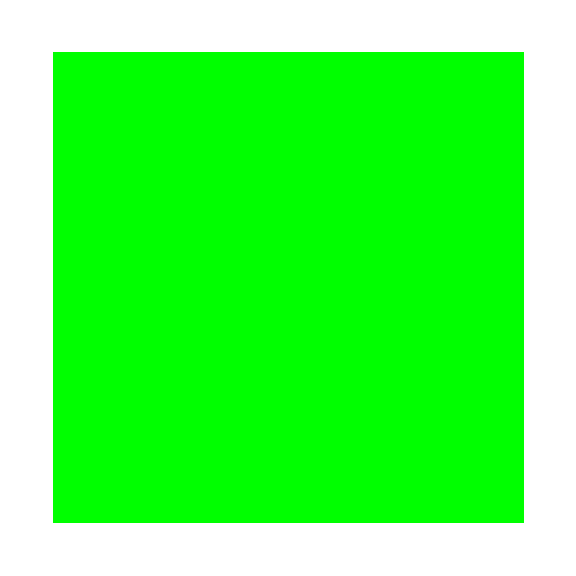

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],Transpose[CovMatrix30x50tabzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

## COVARIANCE MATRIX + OCTUPOLE JOINT 30x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrixOCT50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrixOCT30Bx70FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-30B_70F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrixOCT50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrixOCT30Bx70FzSKA[[1,1,1]]
```

0.0000272876

```mathematica
MultiSplitCovMatrixOCTzSKA = Table[
Join[ArrayFlatten[{{CovMatrixOCT50Bx50FzSKA[[i]], CovMatrixOCT50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrixOCT30x50tabzSKA[[i]], CovMatrixOCT30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixOCTzSKA[[All,325;;648,325;;648]]== CovMatrixOCT30Bx70FzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,1;;324,325;;648]]== CovMatrixOCT50x30tabzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,325;;648,1;;324]]== CovMatrixOCT30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrixOCT50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrixOCT30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrixOCT50x30tabzSKA[[i]] ==CovMatrixOCT30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

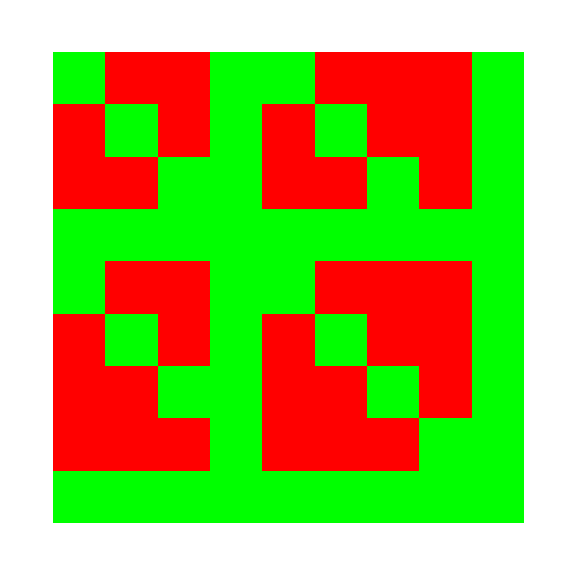

```mathematica
differences=MapThread[Not@*Equal,{CovMatrixOCT50x30tabzSKA[[1]],CovMatrixOCT30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT30x50tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixOCTzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixOCTzSKA[[1]],Transpose[MultiSplitCovMatrixOCTzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

# EXPORT

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,576,576}

{19,648,648}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_all_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_all_50x30_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixOCTzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```